```mathematica
Δ1=Δ2=0

δaI=-g*σ12r-Δ1*ar-f-κ*ai;
δaR=g*σ12i+Δ1*ai−κ*ar;
δp2R=-2*g (σ12ai)+γc ((nc+1) (1−(p2+p1))−nc*p2) "die"
δp1R=2*g (σ12ai)+γh ((nh+1) (1−(p2+p1))−nh*p1)"die"
δσ12aI=g*(p2+(p2−p1)*n)-f*σ12r+Δ1*σ12ar-Δ2*σ12ar−γh/2 nh*σ12ai−γc/2 nc*σ12ai−κ*σ12ai
δσ12aR=f*σ12i-Δ1*σ12r*ai+Δ2*σ12ai−γh/2 nh*σ12ar−γc/2 nc*σ12ar−κ*σ12ar
δσ12I=-g *((p1-p2)*ar)-γc/2*nc*σ12i-γh/2*nh*σ12i "die nid undbeding"
δσ12R=g *((p1-p2)*ai)−γc/2*nc*σ12r−γh/2*nh*σ12r"die"
δnR=2*g (σ12ai)-2*f*ai+2* κ (ncav-n)
𝕏 = {δp2R,δp1R,δσ12aI,δσ12aR,δσ12I,δσ12R,δnR};
```

0

die ((1+nc) (1-p1-p2)-nc p2) γc-2 g σ12ai

die (-nh p1+(1+nh) (1-p1-p2)) γh+2 g σ12ai

g (p2+n (-p1+p2))-(nc γc σ12ai)/2-(nh γh σ12ai)/2-κ σ12ai-f σ12r

-1/2 nc γc σ12ar-(nh γh σ12ar)/2-κ σ12ar+f σ12i

-ar g (p1-p2)-(nc γc σ12i)/2-1/2 die nid undbeding nh γh σ12i

ai g (p1-p2)-(nc γc σ12r)/2-1/2 die nh γh σ12r

-2 ai f+2 (-n+ncav) κ+2 g σ12ai

```mathematica
𝕏p=𝕏/.{Δ1->0,Δ2->0,f->0}
```

{die ((1+nc) (1-p1-p2)-nc p2) γc-2 g σ12ai,die (-nh p1+(1+nh) (1-p1-p2)) γh+2 g σ12ai,g (p2+n (-p1+p2))-(nc γc σ12ai)/2-(nh γh σ12ai)/2-κ σ12ai,-1/2 nc γc σ12ar-(nh γh σ12ar)/2-κ σ12ar,-ar g (p1-p2)-(nc γc σ12i)/2-1/2 die nid undbeding nh γh σ12i,ai g (p1-p2)-(nc γc σ12r)/2-1/2 die nh γh σ12r,2 (-n+ncav) κ+2 g σ12ai}

```mathematica
Solve[𝕏p==0,{σ12r,σ12i,σ12ar,ar,ai,p1,p2,σ12ai,n}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
First[{}]
```

First::nofirst: {} has zero length and no first element.

First[{}]

{{0,0,(nh γc γh+15)/(-2 γc κ-2 nc γc κ-2 γh κ-4 nh γh κ),(γc+11)/(γc+nc γc+γh+2 nh γh),(2 g^2 nc γc^2 γh+67)/(2 (1)),0,0,(nh γc γh+nc nh γc γh-1-(nh 2 (1))/(2 (1))-(3 nc nh γc γh (2 g^2 nc γc^2 γh+67))/(2 (4 g^2 nc γc^2 γh+8+18 g^2 nc nh^2 γc γh^2)))/(-2 g γc-2 g nc γc-2 g γh-4 g nh γh),0},{0,0,6,0}}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
mf[{}]
```

mf[{}]

```mathematica
Clear [γh]
```

```mathematica
γh=γc=γ
γ=1
g=1
nc=ncav=00.02
κ=g/14
```

γ

1

1

0.02

1/14

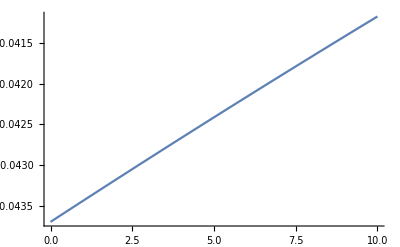

```mathematica
Plot[no[nh],{nh,0,10}]
```

```mathematica
Clear[γc,γh,g,nc,κ,ncav]
```

```mathematica
n[nh_]:=-1*(1/(5050.+5000. nh)(101.-17750. nh-(2.573002775*^9)/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)-(1.68226562*^11 nh)/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)-(1.708870854775*^12 nh^2)/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)-(1.08300140375*^12 nh^3)/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)-(1.7205125*^10 nh^4)/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)+(17675. √(2.1414311129*^10+4.55054179966*^11 nh+5.40081745541*^11 nh^2-1.30157559*^10 nh^3+3.441025*^8 nh^4))/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)+(954275. nh √(2.1414311129*^10+4.55054179966*^11 nh+5.40081745541*^11 nh^2-1.30157559*^10 nh^3+3.441025*^8 nh^4))/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)+(927500. nh^2 √(2.1414311129*^10+4.55054179966*^11 nh+5.40081745541*^11 nh^2-1.30157559*^10 nh^3+3.441025*^8 nh^4))/(-1.9894*^6-1.069082*^8 nh-7.791*^7 nh^2)))
```

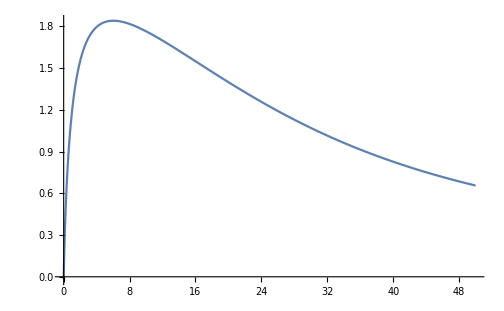

```mathematica
Plot[n[x],{x,0,50}]
```

```mathematica
Clear[γh,γc,f,g,κ,nh,  ncav,nc]
```

```mathematica
Δ1=Δ2=f=0
```

0

```mathematica
δaI=-g*σ12r-Δ1*ar-f-κ*ai;
δaR=g*σ12i+Δ1*ai−κ*ar;
δp2R=-2*g (σ12ai)+γc ((nc+1) (1−(p2+p1))−nc*p2)
δp1R=2*g (σ12ai)+γh ((nh+1) (1−(p2+p1))−nh*p1)
δσ12aI=g*(p2+(p2−p1)*n)-f*σ12r+Δ1*σ12ar-Δ2*σ12ar−γh/2 nh*σ12ai−γc/2 nc*σ12ai−κ*σ21ai;
δσ12aR=f*σ12i-Δ1*σ12ai+Δ2*σ12ai−γh/2 nh*σ12ar−γc/2 nc*σ12ar−κ*σ12ar;
δσ12I=-g *((p1-p2)*ar)-γc/2*nc*σ12i-γh/2*nh*σ12i
δσ12R=g *((p1-p2)*ai)−γc/2*nc*σ12r−γh/2*nh*σ12r
δnR=2*g (σ12ai)-2*f*ai+2* κ (ncav-n);
𝕏 = {δaI,δaR,δp2R,δp1R,δσ12aI,δσ12aR,δσ12I,δσ12R,δnR};
```

((1+nc) (1-p1-p2)-nc p2) γc-2 g σ12ai

(-nh p1+(1+nh) (1-p1-p2)) γh+2 g σ12ai

-ar g (p1-p2)-(nc γc σ12i)/2-(nh γh σ12i)/2

ai g (p1-p2)-(nc γc σ12r)/2-(nh γh σ12r)/2

```mathematica
Solve[δaI==0,σ12r]
```

{{σ12r→-(ai κ)/g}}

```mathematica
Solve[δaR==0,σ12i]
```

{{σ12i→(ar κ)/g}}

```mathematica
Solve[δσ12I==0,σ12i]
```

{{σ12i→-(2 ar g (p1-p2))/(nc γc+nh γh)}}

```mathematica
Solve[-(2 ar g (p1-p2))/(nc γc+nh γh)==(ar κ)/g,ar]
```

{{ar→0}}

```mathematica
First[{{ar->0}}]
```

{ar→0}

WolframAlphaQueryResults

```mathematica
ai=-f/κ;
```

```mathematica
δp2R=-2*g (σ12r*(-ai))+γc ((nc+1) (1−(p2+p1))−nc*p2) ;
δp1R=2*g (σ12r*(-ai))+γh ((nh+1) (1−(p2+p1))−nh*p1);
δσ12I=-g *((p1-p2)*0)-γc/2*nc*σ12i-γh/2*nh*σ12i ;
δσ12R=g *((p1-p2)*ai)−γc/2*nc*σ12r−γh/2*nh*σ12r;
𝕐={δp2R,δp1R,δσ12I,δσ12R};
```

```mathematica
FullSimplify[Solve[𝕐==0,{p1,p2,σ12r,σ12i}]]
```

{{p1→(4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2),p2→(4 f^2 g^2 (γc+nc γc+γh+nh γh)+(1+nc) nh γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2),σ12r→(2 f g (-nc+nh) γc γh κ)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2),σ12i→0}}

```mathematica
p1[nh_]=(4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2);
```

(4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)

```mathematica
p2[nh_]=(4 f^2 g^2 (γc+nc γc+γh+nh γh)+(1+nc) nh γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2);
```

```mathematica
Clear[γh,γc,nc,κ,g,f];
```

```mathematica
p3[nh_]=1-(p1[nh]+p2[nh]);
```

```mathematica
J[nh_]=γh((nh)p2[nh]−(nh+1)*(1-p2[nh]-p1[nh]))
```

(nh (0.04 nh^2+31.36 (2+nh)))/(0.04 nh^2+31.36 (4+3 nh))-(1+nh) (1-(0.+31.36 (2+nh))/(0.04 nh^2+31.36 (4+3 nh))-(0.04 nh^2+31.36 (2+nh))/(0.04 nh^2+31.36 (4+3 nh)))

```mathematica
FullSimplify[%11]
```

(4 f^2 g^2 (-nc+nh) γc γh ωh)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)

γh (-((1+nh) (1-(0.+31.36 f^2 (2+nh))/(0.04 nh^2+31.36 f^2 (4+3 nh))-(0.04 nh^2+31.36 f^2 (2+nh))/(0.04 nh^2+31.36 f^2 (4+3 nh))))+(nh (4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2))/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)) ωh

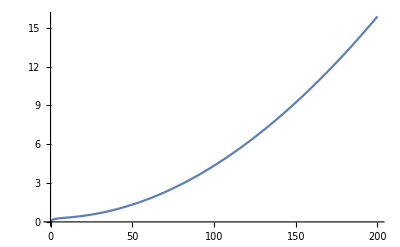

```mathematica
Plot[γh((nh)p2[nh]−(nh+1)*(1-p2[nh]-p1[nh])),{nh,0,200}]
```

```mathematica
γh=γc=1;
nc=0
κ=0.2;
g=2.8;
f=1;
```

0

```mathematica
Plot[J[nh],{nh,0,200}]
```

-Graphics-

```mathematica
γc=gammac
γh=gammah
κ=kappa
Clear[ncav,nc,f,g]
```

gammac

gammah

kappa

```mathematica
FullSimplify[J[nh]]
```

gammah (-(784. nh (1+nh))/(3136.+nh (2352.+1. nh))+(nh (gammac gammah kappa^2 nc (1+nh) (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh)))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh))))

```mathematica
FortranForm[gammah (-(784 nh (1+nh))/(3136+nh (2352+1. nh))+(nh (gammac gammah kappa^2 nc (1+nh) (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh)))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh))))]
```

gammah*((-784*nh*(1 + nh))/(3136 + nh*(2352 + 1.*nh)) + (nh*(gammac*gammah*kappa**2*nc*(1 + nh)*(gammac*nc + gammah*nh) + 4*f**2*g**2*(gammac + gammah + gammac*nc + gammah*nh)))/
     -     (gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh))))

```mathematica
FortranForm[γh ((nh (4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2))/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)-(1+nh) (1-(4 f^2 g^2 (γc+nc γc+γh+nh γh)+(1+nc) nh γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)-(4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)))]
```

gammah*((nh*(gammac*gammah*kappa**2*nc*(1 + nh)*(gammac*nc + gammah*nh) + 4*f**2*g**2*(gammac + gammah + gammac*nc + gammah*nh)))/
     -     (gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh))) - 
     -    (1 + nh)*(1 - (gammac*gammah*kappa**2*(1 + nc)*nh*(gammac*nc + gammah*nh) + 4*f**2*g**2*(gammac + gammah + gammac*nc + gammah*nh))/
     -        (gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh))) - 
     -       (gammac*gammah*kappa**2*nc*(1 + nh)*(gammac*nc + gammah*nh) + 4*f**2*g**2*(gammac + gammah + gammac*nc + gammah*nh))/
     -        (gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh)))))

```mathematica
FullSimplify[γh ((nh (4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2))/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)-(1+nh) (1-(4 f^2 g^2 (γc+nc γc+γh+nh γh)+(1+nc) nh γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)-(4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)))]
```

(4 f^2 g^2 gammac gammah (-nc+nh))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))

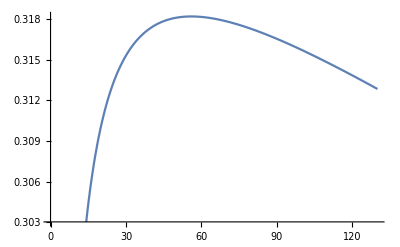

```mathematica
Plot[γh ((nh (4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2))/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)-(1+nh) (1-(4 f^2 g^2 (γc+nc γc+γh+nh γh)+(1+nc) nh γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2)-(4 f^2 g^2 (γc+nc γc+γh+nh γh)+nc (1+nh) γc γh (nc γc+nh γh) κ^2)/(4 f^2 g^2 ((2+3 nc) γc+(2+3 nh) γh)+(nc+nh+3 nc nh) γc γh (nc γc+nh γh) κ^2))),{nh,0,130}]
```

```mathematica
FortranForm[(4 f^2 g^2 gammac gammah (-nc+nh))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))]
```

(4*f**2*g**2*gammac*gammah*(-nc + nh))/(gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh)))

```mathematica
FullSimplify[gammah ((nh (gammac gammah kappa^2 (1+nc) nh (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh)))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))-(1+nh) (1-(gammac gammah kappa^2 (1+nc) nh (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))-(gammac gammah kappa^2 nc (1+nh) (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))))]
```

-(gammac gammah (nc-nh) (4 f^2 g^2+gammah kappa^2 nh (gammac nc+gammah nh)))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))

```mathematica
FortranForm[gammah ((nh (gammac gammah kappa^2 (1+nc) nh (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh)))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))-(1+nh) (1-(gammac gammah kappa^2 (1+nc) nh (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))-(gammac gammah kappa^2 nc (1+nh) (gammac nc+gammah nh)+4 f^2 g^2 (gammac+gammah+gammac nc+gammah nh))/(gammac gammah kappa^2 (gammac nc+gammah nh) (nc+nh+3 nc nh)+4 f^2 g^2 (gammac (2+3 nc)+gammah (2+3 nh)))))]
```

gammah*((nh*(gammac*gammah*kappa**2*(1 + nc)*nh*(gammac*nc + gammah*nh) + 4*f**2*g**2*(gammac + gammah + gammac*nc + gammah*nh)))/
     -     (gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh))) - 
     -    (1 + nh)*(1 - (gammac*gammah*kappa**2*(1 + nc)*nh*(gammac*nc + gammah*nh) + 4*f**2*g**2*(gammac + gammah + gammac*nc + gammah*nh))/
     -        (gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh))) - 
     -       (gammac*gammah*kappa**2*nc*(1 + nh)*(gammac*nc + gammah*nh) + 4*f**2*g**2*(gammac + gammah + gammac*nc + gammah*nh))/
     -        (gammac*gammah*kappa**2*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 4*f**2*g**2*(gammac*(2 + 3*nc) + gammah*(2 + 3*nh)))))